```mathematica
Clear[NN,f]
R[r_]=-(NN[r]*Sin[θ]^2*f''[r]*r^2+2*f[r]*Sin[θ]^2*NN''[r]*r^2+3*NN'[r]*f'[r]*Sin[θ]^2*r^2+6*f'[r]*r*Sin[θ]^2*NN[r]+6*f[r]*NN'[r]*Sin[θ]^2*r+6*f[r]*Sin[θ]^2*NN[r]-4*Sin[θ]^2*NN[r]+2*Cos[θ]^2*NN[r]-2NN[r])/(r^2*Sin[θ]^2*NN[r])
```

1/(r^2 NN[r])Csc[θ]^2 (2 NN[r]-2 Cos[θ]^2 NN[r]+4 NN[r] Sin[θ]^2-6 f[r] NN[r] Sin[θ]^2-6 r NN[r] Sin[θ]^2 f'[r]-6 r f[r] Sin[θ]^2 NN'[r]-3 r^2 Sin[θ]^2 f'[r] NN'[r]-r^2 NN[r] Sin[θ]^2 f''[r]-2 r^2 f[r] Sin[θ]^2 NN''[r])

```mathematica
detg[r_]=NN[r]*r^3*Sin[θ]^2*Sin[ϕ]^2
```

r^3 NN[r] Sin[θ]^2 Sin[ϕ]^2

```mathematica
L[r_]=Simplify[R[r]*detg[r]/(Sin[θ]^2*Sin[ϕ]^2)]
```

-r (NN[r] (-6+6 f[r]+6 r f'[r]+r^2 f''[r])+r (3 r f'[r] NN'[r]+2 f[r] (3 NN'[r]+r NN''[r])))

```mathematica
Collect[L[r],{NN[r],NN'[r],NN''[r]}]
```

-r (6 r f[r]+3 r^2 f'[r]) NN'[r]-r NN[r] (-6+6 f[r]+6 r f'[r]+r^2 f''[r])-2 r^3 f[r] NN''[r]

```mathematica
F0[r_]=6r-6 f[r]*r-6 r^2 *f'[r]-r^3 f''[r]
```

6 r-6 r f[r]-6 r^2 f'[r]-r^3 f''[r]

```mathematica
Integrate[F0[r],r]
```

3 r^2-3 r^2 f[r]-r^3 f'[r]

```mathematica
F2[r_]=-2*r^3*f[r]
```

-2 r^3 f[r]

```mathematica
F1[r_]=-6r^2*f[r]-3r^3*f'[r]
```

-6 r^2 f[r]-3 r^3 f'[r]

```mathematica
Integrate[F0[r],r]-F1[r]+D[F2[r],r]
```

3 r^2-3 r^2 f[r]

```mathematica
Simplify[Solve[3 r^2-3 r^2 f[r]==μ,f[r]]]
```

{{f[r]→1-μ/(3 r^2)}}

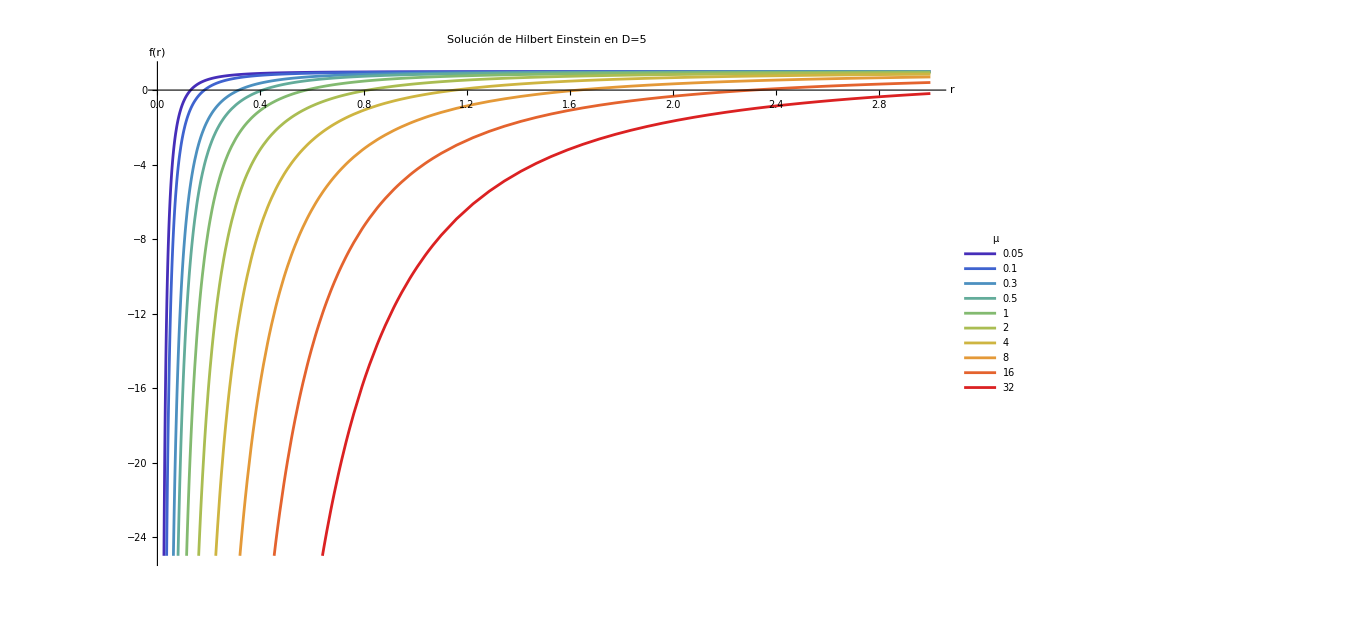

```mathematica
fig4=Plot[Evaluate@Table[1-μ/(3 r^2),{μ,valoresMu}],{r,0,3},PlotRange->{1,-25},PlotStyle->Table[ColorData["Rainbow"][i/Length[valoresMu]],{i,Length[valoresMu]}],PlotLegends->Placed[LineLegend[valoresMu,LegendLabel->Style["μ",18,Bold]],{0.8,0.35}],AxesLabel->{Style["r",18,Bold],Style["f(r)",18,Bold]},PlotLabel->Style["Solución de Hilbert Einstein en D=5",20,Bold],ImageSize->{1000,600}]
```

```mathematica
Export["Hilbert-Einstein 5D.png",fig4]
```

Hilbert-Einstein 5D.png